#### plotting helpers

```mathematica
Do[SetOptions[fcts,BaseStyle->FontSize->14],{fcts,{ListLogLogPlot,ListLogLinearPlot}}]
style[text_]:=Style[text,FontFamily->"Helvetica",FontSize->14,Black]
cbfColors=With[{rgbs=(*{{68,119,170},{204,187,68},{34,136,51},{238,102,119},{102,204,238},{170,51,119}}*){{68,119,170},{221,204,119},{17,119,51},{204,102,119},{136,204,238},{153,153,51},{68,170,153},{170,51,119},{187,187,187}}/255},Map[RGBColor,rgbs]]
```

{RGBColor[{Rational[4, 15], Rational[7, 15], Rational[2, 3]}],RGBColor[{Rational[13, 15], Rational[4, 5], Rational[7, 15]}],RGBColor[{Rational[1, 15], Rational[7, 15], Rational[1, 5]}],RGBColor[{Rational[4, 5], Rational[2, 5], Rational[7, 15]}],RGBColor[{Rational[8, 15], Rational[4, 5], Rational[14, 15]}],RGBColor[{Rational[3, 5], Rational[3, 5], Rational[1, 5]}],RGBColor[{Rational[4, 15], Rational[2, 3], Rational[3, 5]}],RGBColor[{Rational[2, 3], Rational[1, 5], Rational[7, 15]}],RGBColor[{Rational[11, 15], Rational[11, 15], Rational[11, 15]}]}

## Import data from txt files

#### Define the function that convert numbers to the format in file names

```mathematica
number2Printed[number_]:=Module[{returnedString="e",foo,bar,idx,oom},If[number==1,Return["1.0e+00"],If[number==0,Return["0.0e+00"],
If[number<1,
For[idx=1,StringLength[returnedString]==1,idx=idx+1,
foo=Floor[number/10^(-idx)];
If[foo==0,,
bar=Round[(number-foo*10^(-idx))/10^(-idx-1)];
If[StringLength[ToString[idx]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-0",ToString[idx]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-",ToString[idx]]
]
]
];
Return[returnedString]
,
oom=(StringLength[ToString[DecimalForm[Floor[number]*1.]]]-2);
foo=Floor[number/10^oom];
bar=Round[(number-foo*10^oom)/10^(oom-1)];
If[StringLength[ToString[oom]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+0",ToString[oom]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+",ToString[oom]]
];
Return[returnedString]
];
]
]
]
```

#### For not Windows: Import parameters

```mathematica
combinedParameters= ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"combined_parameters.txt"]],{"["->"{","]"->"}"}]];
sequenceLengths= ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"sequence_lengths.txt"]],{"["->"{","]"->"}"}]];
populationSizes=  ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"population_sizes.txt"]],{"["->"{","]"->"}"}]];
```

```mathematica
combinedParameters=Reverse[combinedParameters];
```

#### For Windows: Import parameters

```mathematica
combinedParameters= ToExpression[StringReplace[Import[StringReplace[StringJoin[NotebookDirectory[],"combined_parameters.txt"],{"/"->"\\"}]],{"["->"{","]"->"}"}]];
sequenceLengths= ToExpression[StringReplace[Import[StringReplace[StringJoin[NotebookDirectory[],"sequence_lengths.txt"],{"/"->"\\"}]],{"["->"{","]"->"}"}]];
populationSizes=  ToExpression[StringReplace[Import[StringReplace[StringJoin[NotebookDirectory[],"population_sizes.txt"],{"/"->"\\"}]],{"["->"{","]"->"}"}]];
```

```mathematica
combinedParameters=Reverse[combinedParameters];
```

#### For not Windows: Import data

```mathematica
histograms=Table[Table[Table[Transpose[
ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],number2Printed[combinedParameters[[idx1]]],"_",number2Printed[sequenceLengths[[idx2]]],"_",number2Printed[populationSizes[[idx3]]],".txt"]],{"["->"{","]"->"}"}]]
],{idx3,Length[populationSizes]}],{idx2,Length[sequenceLengths]}],{idx1,Length[combinedParameters]}];
```

#### For Windows: Import data

```mathematica
histograms=Table[Table[Table[Transpose[
ToExpression[StringReplace[Import[StringReplace[StringJoin[NotebookDirectory[],number2Printed[combinedParameters[[idx1]]],"_",number2Printed[sequenceLengths[[idx2]]],"_",number2Printed[populationSizes[[idx3]]],".txt"],{"/"->"\\"}]],{"["->"{","]"->"}"}]]
],{idx3,Length[populationSizes]}],{idx2,Length[sequenceLengths]}],{idx1,Length[combinedParameters]}];
```

## find pdfs given n dynamics, ex: intermediate (SMC’)

```mathematica
pdf=With[{nDynamics=2r-(n[t]-2)/pop},
Simplify[-D[f[t]/.DSolve[{
f'[t]==-(n[t]-1)/pop*f[t]
/.DSolve[{n'[t]==nDynamics,n[0]==2},n[t],t][[1]],
f[0]==1},f[t],t][[1]]/.{t->tau*pop}/.{pop->rho/r},tau]]]
```

ⅇ^(2 rho-2 ⅇ^-tau rho-2 tau) (ⅇ^-tau)^(2 rho) (-2 rho+ⅇ^tau (1+2 rho))

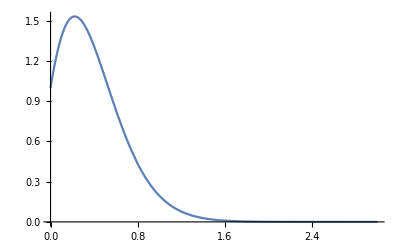

```mathematica
With[{curve=pdf/.rho->3},Plot[curve,{tau,0,3}]]
```

## Plotting

#### Compare the predictions

```mathematica
simple[tau_,rho_]:=(2rho tau+1)Exp[-rho tau^2-tau]
intermediate[tau_,rho_]:=((1+2 rho)Exp[tau]-2 rho) Exp[-2rho Exp[-tau]-2(rho+1)tau+2rho]
complicated[tau_,rho_]:=(-rho Exp[-2tau]+rho+1)Exp[-rho/2*Exp[-2 tau]-(rho+1)tau+rho/2]
```

#### Separate Plots: for comparison

```mathematica
lowestOrder[list_]:=Module[{orders=Floor[Log[10,list]]},Return[N[Round[list/10^orders]*10^orders]]]
lowestOrderFloor[list_]:=Module[{orders=Floor[Log[10,list]]},Return[N[Floor[list/10^orders]*10^orders]]]
```

```mathematica
histogramsFlatten=Flatten[Table[Table[Table[histograms[[combinedParameterIdx,sequenceLengthIdx,populationSizeIdx]],{populationSizeIdx,Length[populationSizes]}],{sequenceLengthIdx,Length[sequenceLengths]}],{combinedParameterIdx,Length[combinedParameters]}],{{1},{2,3}}];
colors=Table[(*CMYKColor[idx1/8,idx1/8,0.,0.1]*)Hue[idx1/Length[populationSizes],0.5,0.8],{idx1,Length[populationSizes]}];
ranges=Table[Max[Flatten[histogramsFlatten[[combinedParameterIdx,;;,;;,1]]]],{combinedParameterIdx,Length[combinedParameters]}];
smallTicks=Table[{{0,lowestOrderFloor[ranges[[combinedParameterIdx]]]/2,lowestOrderFloor[ranges[[combinedParameterIdx]]]},{1,0.1,0.01}},{combinedParameterIdx,Length[combinedParameters]}];
```

```mathematica
Grid[{{Rotate[style["probability density p(τ) for finding MRCA"],Pi/2],Grid[ArrayReshape[Table[Grid[{{style[StringJoin["ρ = ",ToString[combinedParameters[[combinedParameterIdx]]]]]},{ListPlot[histogramsFlatten[[combinedParameterIdx]],PlotStyle->Flatten[colors],PlotRange->All,Epilog->Inset[ListLogPlot[histogramsFlatten[[combinedParameterIdx]],PlotRange->All,Ticks->smallTicks[[combinedParameterIdx]],PlotStyle->Flatten[colors]],{Right,Top},{Right,Top},Scaled[Table[0.6,2]]]]}}],{combinedParameterIdx,Length[combinedParameters]}],{2,Length[combinedParameters]/2}],Frame->All],
Grid[{{style["population"]},{style["size"]},{Grid[Transpose[{colors,Table[If[IntegerQ[Log[10,populationSize]],Superscript["10",ToString[Log[10,populationSize]]],],{populationSize,populationSizes}]}]]}}]},{,style["rescaled time τ"],}}]
Export["fig5.5 - collapse big.pdf",%]
```

probability density p(τ) for finding MRCA | ρ = 0
-Graphics- | ρ = 1
-Graphics- | ρ = 10
-Graphics-
ρ = 30
-Graphics- | ρ = 100
-Graphics- | ρ = 300
-Graphics- | population
size
Hue[Rational[1, 9], 0.5, 0.8] | 10^1
Hue[Rational[2, 9], 0.5, 0.8] | 
Hue[Rational[1, 3], 0.5, 0.8] | 
Hue[Rational[4, 9], 0.5, 0.8] | 
Hue[Rational[5, 9], 0.5, 0.8] | 10^2
Hue[Rational[2, 3], 0.5, 0.8] | 
Hue[Rational[7, 9], 0.5, 0.8] | 
Hue[Rational[8, 9], 0.5, 0.8] | 
Hue[1, 0.5, 0.8] | 10^3
 | rescaled time τ |

fig5.5 - collapse big.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fig5.5 - collapse big.pdf"]]]
```

#### Separate Plots: compare to data

```mathematica
histogramsFlattenFlatten=Flatten[histogramsFlatten,{{1},{2,3}}];
ranges=Table[Max[histogramsFlattenFlatten[[combinedParameterIdx,;;,1]]],{combinedParameterIdx,Length[combinedParameters]}];
```

```mathematica
With[{simples=Table[simple[tau,combinedParameters[[combinedParameterIdx]]],{combinedParameterIdx,Length[combinedParameters]}],intermediates=Table[intermediate[tau,combinedParameters[[combinedParameterIdx]]],{combinedParameterIdx,Length[combinedParameters]}],complicateds=Table[complicated[tau,combinedParameters[[combinedParameterIdx]]],{combinedParameterIdx,Length[combinedParameters]}]},Grid[{{Rotate[style["probability density p(τ) for finding MRCA"],Pi/2],Grid[ArrayReshape[Table[Grid[{{style[StringJoin["ρ = ",ToString[combinedParameters[[combinedParameterIdx]]]]]},{Show[ListPlot[histogramsFlattenFlatten[[combinedParameterIdx]],PlotRange->All,PlotStyle->cbfColors[[1]]],Plot[{simples[[combinedParameterIdx]],intermediates[[combinedParameterIdx]],complicateds[[combinedParameterIdx]]},{tau,0,ranges[[combinedParameterIdx]]},PlotRange->All,PlotStyle->Transpose[{cbfColors[[2;;4]],Table[Thickness[0.008],3]}]],Epilog->Inset[Show[ListLogPlot[histogramsFlattenFlatten[[combinedParameterIdx]],PlotRange->All,Ticks->smallTicks[[combinedParameterIdx]],PlotStyle->cbfColors[[1]]],
LogPlot[{simples[[combinedParameterIdx]],intermediates[[combinedParameterIdx]],complicateds[[combinedParameterIdx]]},{tau,0,ranges[[combinedParameterIdx]]},PlotRange->All,PlotStyle->Transpose[{cbfColors[[2;;4]],Table[Thickness[0.02],3]}]]],{Right,Top},{Right,Top},Scaled[Table[0.6,2]]]]}}],{combinedParameterIdx,Length[combinedParameters]}],{2,Length[combinedParameters]/2}],Frame->All],
Grid[Transpose[{cbfColors[[1;;4]],Table[style[text],{text,{"simulation","SMC","SMC'","SMC+"}}]}]]},{,style["rescaled time τ"],}}]]
Export["fig5 - compare big.pdf",%]
```

probability density p(τ) for finding MRCA | ρ = 0
-Graphics- | ρ = 1
-Graphics- | ρ = 10
-Graphics-
ρ = 30
-Graphics- | ρ = 100
-Graphics- | ρ = 300
-Graphics- | RGBColor[{Rational[4, 15], Rational[7, 15], Rational[2, 3]}] | simulation
RGBColor[{Rational[13, 15], Rational[4, 5], Rational[7, 15]}] | SMC
RGBColor[{Rational[1, 15], Rational[7, 15], Rational[1, 5]}] | SMC'
RGBColor[{Rational[4, 5], Rational[2, 5], Rational[7, 15]}] | SMC+
 | rescaled time τ |

fig5 - compare big.pdf

#### first two cumulant comparisons combined (smooth)

```mathematica
xValues=combinedParameters;
ticks=Automatic;
rhos=Table[Exp[(logRhoIdx-21)/200.*Log[500.]],{logRhoIdx,221}];
means=Table[Table[{xValues[[combinedParameterIdx]],Total[histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,1]]*histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]/Total[histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]},{detailedParametersIdx,Length[populationSizes]*Length[sequenceLengths]}],{combinedParameterIdx,Length[combinedParameters]}];
vars=Table[Table[{xValues[[combinedParameterIdx]],Total[(histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,1]]-means[[combinedParameterIdx,detailedParametersIdx,2]])^2*histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]/Total[histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]},{detailedParametersIdx,Length[populationSizes]*Length[sequenceLengths]}],{combinedParameterIdx,Length[combinedParameters]}];
stds=Table[Table[{xValues[[combinedParameterIdx]],Sqrt[vars[[combinedParameterIdx,detailedParametersIdx,2]]]},{detailedParametersIdx,Length[populationSizes]*Length[sequenceLengths]}],{combinedParameterIdx,Length[combinedParameters]}];
meansSummarized=Table[Mean[means[[combinedParameterIdx,;;,2]]],{combinedParameterIdx,Length[combinedParameters]}];
varsSummarized=Table[Mean[vars[[combinedParameterIdx,;;,2]]],{combinedParameterIdx,Length[combinedParameters]}];
stdsSummarized=Table[Mean[stds[[combinedParameterIdx,;;,2]]],{combinedParameterIdx,Length[combinedParameters]}];
meanSimpleSmooth=Table[{rho,NIntegrate[simple[tau,rho]*tau,{tau,0,Infinity}]},{rho,rhos}];
varSimpleSmooth=Transpose[{rhos,NIntegrate[simple[tau,rhos]*(tau-meanSimpleSmooth[[;;,2]])^2,{tau,0,Infinity}]}];
stdSimpleSmooth=Transpose[{rhos,Sqrt[varSimpleSmooth[[;;,2]]]}];
meanIntermediateSmooth=Table[{rho,NIntegrate[intermediate[tau,rho]*tau,{tau,0,Infinity}]},{rho,rhos}];
varIntermediateSmooth=Transpose[{rhos,NIntegrate[intermediate[tau,rhos]*(tau-meanIntermediateSmooth[[;;,2]])^2,{tau,0,Infinity}]}];
stdIntermediateSmooth=Transpose[{rhos,Sqrt[varIntermediateSmooth[[;;,2]]]}];
meanComplicatedSmooth=Table[{rho,NIntegrate[complicated[tau,rho]*tau,{tau,0,Infinity}]},{rho,rhos}];
varComplicatedSmooth=Transpose[{rhos,NIntegrate[complicated[tau,rhos]*(tau-meanComplicatedSmooth[[;;,2]])^2,{tau,0,Infinity}]}];
stdComplicatedSmooth=Transpose[{rhos,Sqrt[varComplicatedSmooth[[;;,2]]]}];
meanAsymptoticSmooth=Table[{rho,Sqrt[Pi]/2/Sqrt[rho]},{rho,rhos}];
varAsymptoticSmooth=Table[{rho,(4-Pi)/4/rho},{rho,rhos}];
stdAsymptoticSmooth=Transpose[{rhos,Sqrt[varAsymptoticSmooth[[;;,2]]]}];
```

```mathematica
meansSimple=Transpose[{xValues,NIntegrate[simple[tau,combinedParameters*1.]*tau,{tau,0,Infinity}]}];
varsSimple=Transpose[{xValues,NIntegrate[simple[tau,combinedParameters*1.]*(tau-meansSimple[[;;,2]])^2,{tau,0,Infinity}]}];
stdsSimple=Transpose[{xValues,Sqrt[varsSimple[[;;,2]]]}];
meansIntermediate=Transpose[{xValues,NIntegrate[intermediate[tau,combinedParameters*1.]*tau,{tau,0,Infinity}]}];
varsIntermediate=Transpose[{xValues,NIntegrate[intermediate[tau,combinedParameters*1.]*(tau-meansIntermediate[[;;,2]])^2,{tau,0,Infinity}]}];
stdsIntermediate=Transpose[{xValues,Sqrt[varsIntermediate[[;;,2]]]}];
meansComplicated=Transpose[{xValues,NIntegrate[complicated[tau,combinedParameters*1.]*tau,{tau,0,Infinity}]}];
varsComplicated=Transpose[{xValues,NIntegrate[complicated[tau,combinedParameters*1.]*(tau-meansComplicated[[;;,2]])^2,{tau,0,Infinity}]}];
stdsComplicated=Transpose[{xValues,Sqrt[varsComplicated[[;;,2]]]}];
meansAsymptotic=Transpose[{xValues[[2;;]],Sqrt[Pi]/2/Sqrt[combinedParameters[[2;;]]]}];
varsAsymptotic=Transpose[{xValues[[2;;]],(4-Pi)/4/combinedParameters[[2;;]]}];
stdsAsymptotic=Transpose[{xValues[[2;;]],Sqrt[varsAsymptotic[[;;,2]]]}];
meanErrorRsSimple=Transpose[{xValues,(meansSimple[[;;,2]]-meansSummarized)/meansSummarized}];
varErrorRsSimple=Transpose[{xValues,(varsSimple[[;;,2]]-varsSummarized)/varsSummarized}];
stdErrorRsSimple=Transpose[{xValues,(stdsSimple[[;;,2]]-stdsSummarized)/stdsSummarized}];
meanErrorRsIntermediate=Transpose[{xValues,(meansIntermediate[[;;,2]]-meansSummarized)/meansSummarized}];
varErrorRsIntermediate=Transpose[{xValues,(varsIntermediate[[;;,2]]-varsSummarized)/varsSummarized}];
stdErrorRsIntermediate=Transpose[{xValues,(stdsIntermediate[[;;,2]]-stdsSummarized)/stdsSummarized}];
meanErrorRsComplicated=Transpose[{xValues,(meansComplicated[[;;,2]]-meansSummarized)/meansSummarized}];
varErrorRsComplicated=Transpose[{xValues,(varsComplicated[[;;,2]]-varsSummarized)/varsSummarized}];
stdErrorRsComplicated=Transpose[{xValues,(stdsComplicated[[;;,2]]-stdsSummarized)/stdsSummarized}];
meanErrorRsAsymptotic=Transpose[{xValues[[2;;]],(meansAsymptotic[[;;,2]]-meansSummarized[[2;;]])/meansSummarized[[2;;]]}];
varErrorRsAsymptotic=Transpose[{xValues[[2;;]],(varsAsymptotic[[;;,2]]-varsSummarized[[2;;]])/varsSummarized[[2;;]]}];
stdErrorRsAsymptotic=Transpose[{xValues[[2;;]],(stdsAsymptotic[[;;,2]]-stdsSummarized[[2;;]])/stdsSummarized[[2;;]]}];
```

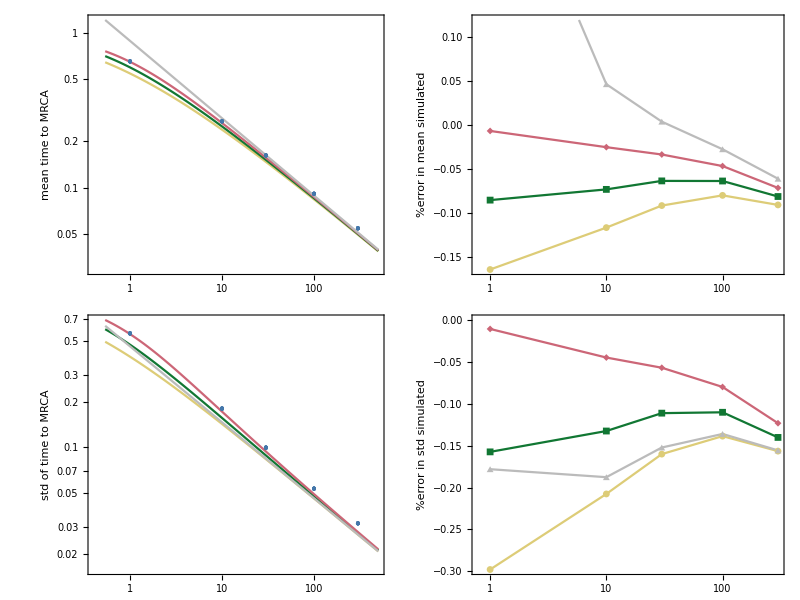
-Graphics- | RGBColor[{Rational[4, 15], Rational[7, 15], Rational[2, 3]}] |  simulation 
RGBColor[{Rational[13, 15], Rational[4, 5], Rational[7, 15]}] | SMC
RGBColor[{Rational[1, 15], Rational[7, 15], Rational[1, 5]}] | SMC'
RGBColor[{Rational[4, 5], Rational[2, 5], Rational[7, 15]}] | SMC+
RGBColor[{Rational[11, 15], Rational[11, 15], Rational[11, 15]}] | asymptotic
rescaled map length ρ |

fig2 - 3 predictions (std).pdf

```mathematica
Grid[{{Grid[Transpose[{{ListLogLogPlot[{Flatten[means,{{1,2}}],meanSimpleSmooth,meanIntermediateSmooth,meanComplicatedSmooth,meanAsymptoticSmooth},Joined->Join[{False},Table[True,4]],PlotMarkers->Join[{{Automatic,Tiny}},Table[None,4]],ImageSize->Medium,Ticks->ticks,Frame->True,FrameLabel->{None,style["mean time to MRCA"]},PlotStyle->Join[cbfColors[[1;;4]],{cbfColors[[-1]]}]],
ListLogLogPlot[{Flatten[stds,{{1,2}}],stdSimpleSmooth,stdIntermediateSmooth,stdComplicatedSmooth,stdAsymptoticSmooth},Joined->Join[{False},Table[True,4]],PlotMarkers->Join[{{Automatic,Tiny}},Table[None,4]],ImageSize->Medium,Ticks->ticks,Frame->True,FrameLabel->{None,style["std of time to MRCA"]},PlotStyle->Join[cbfColors[[1;;4]],{cbfColors[[-1]]}]]},{ListLogLinearPlot[{meanErrorRsSimple,meanErrorRsIntermediate,meanErrorRsComplicated,meanErrorRsAsymptotic},Joined->True,PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotStyle->Join[cbfColors[[2;;4]],{cbfColors[[-1]]}],Ticks->ticks,Frame->True,FrameLabel->{{style["%error in mean simulated"]," "},{None,None}}],
ListLogLinearPlot[{stdErrorRsSimple,stdErrorRsIntermediate,stdErrorRsComplicated,stdErrorRsAsymptotic},Joined->True,PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotStyle->Join[cbfColors[[2;;4]],{cbfColors[[-1]]}],Ticks->ticks,Frame->True,FrameLabel->{{style["%error in std simulated"]," "},{None,None}}]}}]],
Grid[Transpose[{Join[cbfColors[[1;;4]],{cbfColors[[-1]]}],Table[style[text],{text,{" simulation ","SMC","SMC'","SMC+", "asymptotic"}}]}]]},{Style["rescaled map length ρ",FontFamily->"Helvetica",FontSize->14],}}]
Export["fig2 - 3 predictions (std).pdf",%]
```

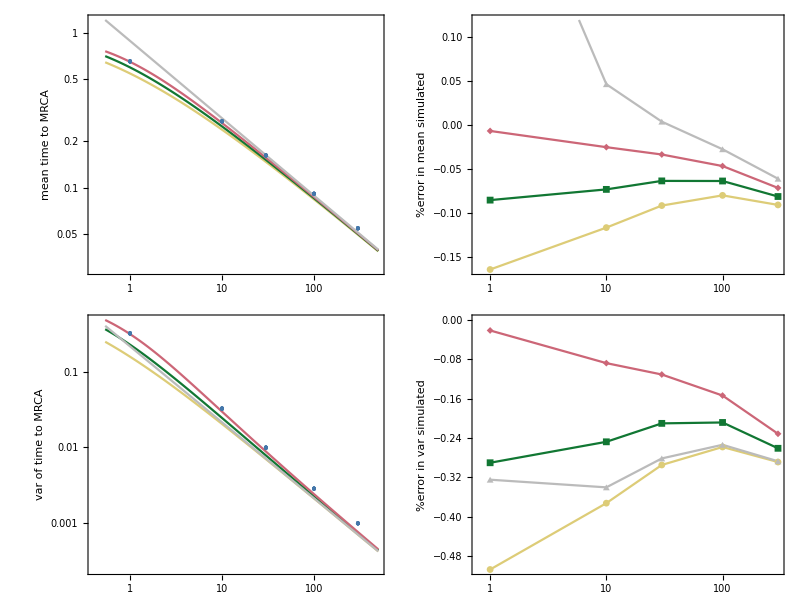
-Graphics- | RGBColor[{Rational[4, 15], Rational[7, 15], Rational[2, 3]}] |  simulation 
RGBColor[{Rational[13, 15], Rational[4, 5], Rational[7, 15]}] | SMC
RGBColor[{Rational[1, 15], Rational[7, 15], Rational[1, 5]}] | SMC'
RGBColor[{Rational[4, 5], Rational[2, 5], Rational[7, 15]}] | SMC+
RGBColor[{Rational[11, 15], Rational[11, 15], Rational[11, 15]}] | asymptotic
rescaled map length ρ |

fig2.1 - 3 predictions (var).pdf

```mathematica
Grid[{{Grid[Transpose[{{ListLogLogPlot[{Flatten[means,{{1,2}}],meanSimpleSmooth,meanIntermediateSmooth,meanComplicatedSmooth,meanAsymptoticSmooth},Joined->Join[{False},Table[True,4]],PlotMarkers->Join[{{Automatic,Tiny}},Table[None,4]],ImageSize->Medium,Ticks->ticks,Frame->True,FrameLabel->{None,style["mean time to MRCA"]},PlotStyle->Join[cbfColors[[1;;4]],{cbfColors[[-1]]}]],
ListLogLogPlot[{Flatten[vars,{{1,2}}],varSimpleSmooth,varIntermediateSmooth,varComplicatedSmooth,varAsymptoticSmooth},Joined->Join[{False},Table[True,4]],PlotMarkers->Join[{{Automatic,Tiny}},Table[None,4]],ImageSize->Medium,Ticks->ticks,Frame->True,FrameLabel->{None,style["var of time to MRCA"]},PlotStyle->Join[cbfColors[[1;;4]],{cbfColors[[-1]]}]]},{ListLogLinearPlot[{meanErrorRsSimple,meanErrorRsIntermediate,meanErrorRsComplicated,meanErrorRsAsymptotic},Joined->True,PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotStyle->Join[cbfColors[[2;;4]],{cbfColors[[-1]]}],Ticks->ticks,Frame->True,FrameLabel->{{style["%error in mean simulated"]," "},{None,None}}],
ListLogLinearPlot[{varErrorRsSimple,varErrorRsIntermediate,varErrorRsComplicated,varErrorRsAsymptotic},Joined->True,PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotStyle->Join[cbfColors[[2;;4]],{cbfColors[[-1]]}],Ticks->ticks,Frame->True,FrameLabel->{{style["%error in var simulated"]," "},{None,None}}]}}]],
Grid[Transpose[{Join[cbfColors[[1;;4]],{cbfColors[[-1]]}],Table[style[text],{text,{" simulation ","SMC","SMC'","SMC+", "asymptotic"}}]}]]},{Style["rescaled map length ρ",FontFamily->"Helvetica",FontSize->14],}}]
Export["fig2.1 - 3 predictions (var).pdf",%]
```

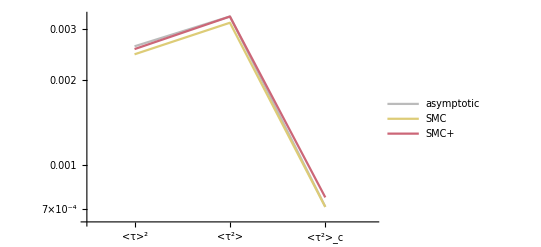

fig2.9 - moments.pdf

```mathematica
ListLogPlot[{{meansAsymptotic[[-1,2]]^2,varsAsymptotic[[-1,2]]+meansAsymptotic[[-1,2]]^2,varsAsymptotic[[-1,2]]},{meansSimple[[-1,2]]^2,varsSimple[[-1,2]]+meansSimple[[-1,2]]^2,varsSimple[[-1,2]]},{meansComplicated[[-1,2]]^2,varsComplicated[[-1,2]]+meansComplicated[[-1,2]]^2,varsComplicated[[-1,2]]}},Joined->True,PlotLegends->{"asymptotic","SMC","SMC+"},Ticks->{{{1,"<τ>^2"},{2,"<τ^2>"},{3,"<τ^2>_c"}},Automatic},PlotStyle->cbfColors[[{-1,2,4}]],PlotRange->{{0.5,3.5},Full}]
Export["fig2.9 - moments.pdf",%]
```

#### exact (will take a long time to integrate exactly)

```mathematica
meanSimpleExactFree=Integrate[simple[tau,rho]*tau,{tau,0,Infinity}]
meanIntermediateExactFree=Integrate[intermediate[tau,rho]*tau,{tau,0,Infinity}]
meanComplicatedExactFree=Integrate[complicated[tau,rho]*tau,{tau,0,Infinity}]
meansqSimpleExactFree=Integrate[simple[tau,rho]*tau^2,{tau,0,Infinity}]
meansqIntermediateExactFree=Integrate[intermediate[tau,rho]*tau^2,{tau,0,Infinity}]
meansqComplicatedExactFree=Integrate[complicated[tau,rho]*tau^2,{tau,0,Infinity}]
```

ConditionalExpression[(ⅇ^(1/4/rho) √π Erfc[1/(2 √rho)])/(2 √rho), Re[rho]≥0]

ConditionalExpression[(ⅇ/2)^(2 rho) rho^(-2 rho) (Gamma[2 rho]+MeijerG[{{},{0,0}},{{-1,-1,2 rho},{}},2 rho]-MeijerG[{{},{0,0}},{{-1,-1,1+2 rho},{}},2 rho]+MeijerG[{{},{1,1}},{{0,0,1+2 rho},{}},2 rho]), Re[rho]>-1/2]

ConditionalExpression[1/(1+rho)2^(1/2 (-3+rho)) ⅇ^(rho/2) rho^(1/2 (-1-rho)) (MeijerG[{{},{1,1}},{{0,0,(1+rho)/2},{}},rho/2]-2 MeijerG[{{},{1,1}},{{0,0,(3+rho)/2},{}},rho/2]+4 (Gamma[(3+rho)/2]+MeijerG[{{},{2,2}},{{1,1,(3+rho)/2},{}},rho/2]-MeijerG[{{},{2,2}},{{1,1,(5+rho)/2},{}},rho/2]+MeijerG[{{},{3,3}},{{2,2,(5+rho)/2},{}},rho/2])), Re[rho]>-1]

ConditionalExpression[1/rho-(ⅇ^(1/4/rho) √π Erfc[1/(2 √rho)])/(2 rho^(3/2)), Re[rho]≥0]

ConditionalExpression[1/(1+2 rho)(ⅇ/2)^(2 rho) rho^(-1-2 rho) (Gamma[1+2 rho] Log[2]+rho Gamma[1+2 rho] Log[4]+Gamma[1+2 rho] Log[rho]+2 rho Gamma[1+2 rho] Log[rho]+MeijerG[{{},{1,1,1}},{{0,0,0,2 (1+rho)},{}},2 rho]-MeijerG[{{},{1,1,1}},{{0,0,0,1+2 rho},{}},2 rho]-2 MeijerG[{{},{2,2,2}},{{1,1,1,2 (1+rho)},{}},2 rho]+MeijerG[{{},{2,2,2}},{{1,1,1,3+2 rho},{}},2 rho]-MeijerG[{{},{3,3,3}},{{2,2,2,3+2 rho},{}},2 rho]-Gamma[1+2 rho] PolyGamma[0,1+2 rho]-2 rho Gamma[1+2 rho] PolyGamma[0,1+2 rho]), Re[rho]>-1/2]

ConditionalExpression[-1/(1+rho)^2 2^(1/2 (-3+rho)) ⅇ^(rho/2) rho^(-1/2-rho/2) (MeijerG[{{},{1,1,1}},{{0,0,0,(1+rho)/2},{}},rho/2]+2 (Gamma[(1+rho)/2] Log[2]+2 rho Gamma[(1+rho)/2] Log[2]+rho^2 Gamma[(1+rho)/2] Log[2]-Gamma[(1+rho)/2] Log[rho]-2 rho Gamma[(1+rho)/2] Log[rho]-rho^2 Gamma[(1+rho)/2] Log[rho]-MeijerG[{{},{1,1,1}},{{0,0,0,(3+rho)/2},{}},rho/2]+3 MeijerG[{{},{2,2,2}},{{1,1,1,(3+rho)/2},{}},rho/2]-4 MeijerG[{{},{2,2,2}},{{1,1,1,(5+rho)/2},{}},rho/2]+6 MeijerG[{{},{3,3,3}},{{2,2,2,(5+rho)/2},{}},rho/2]-4 MeijerG[{{},{3,3,3}},{{2,2,2,(7+rho)/2},{}},rho/2]+4 MeijerG[{{},{4,4,4}},{{3,3,3,(7+rho)/2},{}},rho/2]+Gamma[(1+rho)/2] PolyGamma[0,(1+rho)/2]+2 rho Gamma[(1+rho)/2] PolyGamma[0,(1+rho)/2]+rho^2 Gamma[(1+rho)/2] PolyGamma[0,(1+rho)/2])), Re[rho]>-1]

```mathematica
meanSimpleExact[foo_]:=Refine[(meanSimpleExactFree/.rho->foo),foo>0]
meanIntermediateExact[foo_]:=Refine[(meanIntermediateExactFree/.rho->foo),foo>0]
meanComplicatedExact[foo_]:=Refine[(meanComplicatedExactFree/.rho->foo),foo>0]
meansqSimpleExact[foo_]:=Refine[(meansqSimpleExactFree/.rho->foo),foo>0]
meansqIntermediateExact[foo_]:=Refine[(meansqIntermediateExactFree/.rho->foo),foo>0]
meansqComplicatedExact[foo_]:=Refine[(meansqComplicatedExactFree/.rho->foo),foo>0]
```

```mathematica
limMeanSimpleO1=Limit[meanSimpleExact[rho]*Sqrt[rho],rho->Infinity]
limMeanIntermediateO1=Limit[meanIntermediateExact[rho]*Sqrt[rho],rho->Infinity]
limMeanComplicatedO1=Limit[meanComplicatedExact[rho]*Sqrt[rho],rho->Infinity]
limMeansqSimpleO1=Limit[meansqSimpleExact[rho]*rho,rho->Infinity]
limMeansqIntermediateO1=Limit[meansqIntermediateExact[rho]*rho,rho->Infinity]
limMeansqComplicatedO1=Limit[meansqComplicatedExact[rho]*rho,rho->Infinity]
```

(√π)/2

√π

√π

1

$Aborted

$Aborted

```mathematica
rhos=Table[Exp[(logRhoIdx-21)/200.*Log[500.]],{logRhoIdx,221}];
Quiet[meanSimpleExactSmooth=Table[{rho,meanSimpleExact[rho]},{rho,rhos}];
varSimpleExactSmooth=Table[{rho,meansqSimpleExact[rho]-meanSimpleExactSmooth[[logRhoIdx,2]]^2},{rho,rhos}];
meanIntermediateExactSmooth=Table[{rho,meanIntermediateExact[rho]},{rho,rhos}];
varIntermediateExactSmooth=Table[{rho,meansqIntermediateExact[rho]-meanIntermediateExactSmooth[[logRhoIdx,2]]^2},{rho,rhos}];
meanComplicatedExactSmooth=Table[{rho,meanComplicatedExact[rho]},{rho,rhos}];
varComplicatedExactSmooth=Table[{rho,meansqComplicatedExact[rho]-meanComplicatedExactSmooth[[logRhoIdx,2]]^2},{rho,rhos}];]
```

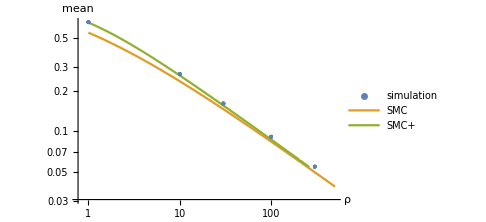
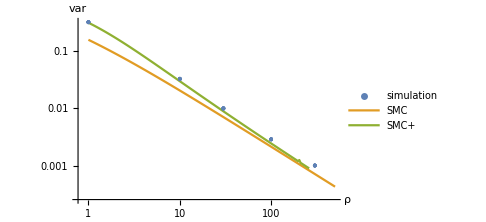
-Graphics- | -Graphics-

```mathematica
Grid[{{ListLogLogPlot[{Flatten[means,{{1,2}}],meanSimpleExactSmooth,meanIntermediateExactSmooth,meanComplicatedExactSmooth},Joined->{False,True,True},ImageSize->Medium,PlotLegends->{"simulation","SMC","SMC'","SMC+"},Ticks->ticks,AxesLabel->{"ρ","mean"}],
ListLogLogPlot[{Flatten[vars,{{1,2}}],varSimpleExactSmooth,varIntermediateExactSmooth,varComplicatedExactSmooth},Joined->{False,True,True},ImageSize->Medium,PlotLegends->{"simulation","SMC","SMC'","SMC+"},Ticks->ticks,AxesLabel->{"ρ","var"}]}}]
```

#### discrete

```mathematica
xValues=Table[combinedParameterIdx,{combinedParameterIdx,Length[combinedParameters]}];
ticks={Transpose[{xValues,combinedParameters}],Automatic};
means=Table[Table[{xValues[[combinedParameterIdx]],Total[histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,1]]*histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]/Total[histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]},{detailedParametersIdx,Length[populationSizes]*Length[sequenceLengths]}],{combinedParameterIdx,Length[combinedParameters]}];
vars=Table[Table[{xValues[[combinedParameterIdx]],Total[(histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,1]]-means[[combinedParameterIdx,detailedParametersIdx,2]])^2*histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]/Total[histogramsFlatten[[combinedParameterIdx,detailedParametersIdx]][[;;,2]]]},{detailedParametersIdx,Length[populationSizes]*Length[sequenceLengths]}],{combinedParameterIdx,Length[combinedParameters]}];
meansSummarized=Table[Mean[means[[combinedParameterIdx,;;,2]]],{combinedParameterIdx,Length[combinedParameters]}];
varsSummarized=Table[Mean[vars[[combinedParameterIdx,;;,2]]],{combinedParameterIdx,Length[combinedParameters]}];
meansSimple=Table[{xValues[[combinedParameterIdx]],NIntegrate[simple[tau,combinedParameters[[combinedParameterIdx]]*1.]*tau,{tau,0,Infinity}]},{combinedParameterIdx,Length[combinedParameters]}];
varsSimple=Table[{xValues[[combinedParameterIdx]],NIntegrate[simple[tau,combinedParameters[[combinedParameterIdx]]*1.]*(tau-meansSimple[[combinedParameterIdx,2]])^2,{tau,0,Infinity}]},{combinedParameterIdx,Length[combinedParameters]}];
meansIntermediate=Table[{xValues[[combinedParameterIdx]],NIntegrate[intermediate[tau,combinedParameters[[combinedParameterIdx]]*1.]*tau,{tau,0,Infinity}]},{combinedParameterIdx,Length[combinedParameters]}];
varsIntermediate=Table[{xValues[[combinedParameterIdx]],NIntegrate[intermediate[tau,combinedParameters[[combinedParameterIdx]]*1.]*(tau-meansIntermediate[[combinedParameterIdx,2]])^2,{tau,0,Infinity}]},{combinedParameterIdx,Length[combinedParameters]}];
meansComplicated=Table[{xValues[[combinedParameterIdx]],NIntegrate[complicated[tau,combinedParameters[[combinedParameterIdx]]*1.]*tau,{tau,0,Infinity}]},{combinedParameterIdx,Length[combinedParameters]}];
varsComplicated=Table[{xValues[[combinedParameterIdx]],NIntegrate[complicated[tau,combinedParameters[[combinedParameterIdx]]*1.]*(tau-meansComplicated[[combinedParameterIdx,2]])^2,{tau,0,Infinity}]},{combinedParameterIdx,Length[combinedParameters]}];
meanErrorRsSimple=Table[{xValues[[combinedParameterIdx]],(meansSimple[[combinedParameterIdx,2]]-meansSummarized[[combinedParameterIdx]])/meansSummarized[[combinedParameterIdx]]},{combinedParameterIdx,Length[combinedParameters]}];
meanErrorRsIntermediate=Table[{xValues[[combinedParameterIdx]],(meansIntermediate[[combinedParameterIdx,2]]-meansSummarized[[combinedParameterIdx]])/meansSummarized[[combinedParameterIdx]]},{combinedParameterIdx,Length[combinedParameters]}];
meanErrorRsComplicated=Table[{xValues[[combinedParameterIdx]],(meansComplicated[[combinedParameterIdx,2]]-meansSummarized[[combinedParameterIdx]])/meansSummarized[[combinedParameterIdx]]},{combinedParameterIdx,Length[combinedParameters]}];
varErrorRsSimple=Table[{xValues[[combinedParameterIdx]],(varsSimple[[combinedParameterIdx,2]]-varsSummarized[[combinedParameterIdx]])/varsSummarized[[combinedParameterIdx]]},{combinedParameterIdx,Length[combinedParameters]}];
varErrorRsIntermediate=Table[{xValues[[combinedParameterIdx]],(varsIntermediate[[combinedParameterIdx,2]]-varsSummarized[[combinedParameterIdx]])/varsSummarized[[combinedParameterIdx]]},{combinedParameterIdx,Length[combinedParameters]}];
varErrorRsComplicated=Table[{xValues[[combinedParameterIdx]],(varsComplicated[[combinedParameterIdx,2]]-varsSummarized[[combinedParameterIdx]])/varsSummarized[[combinedParameterIdx]]},{combinedParameterIdx,Length[combinedParameters]}];
```

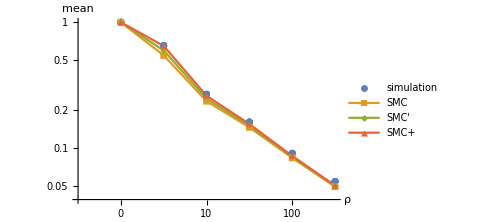
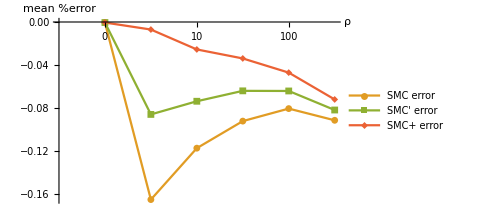
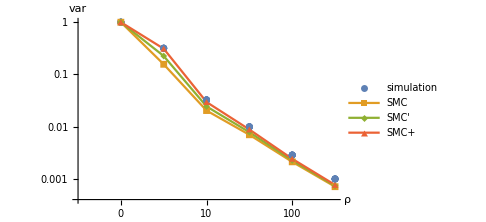
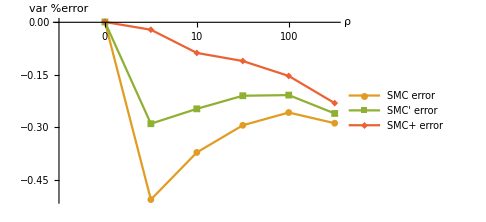
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{ListLogPlot[{Flatten[means,{{1,2}}],meansSimple,meansIntermediate,meansComplicated},Joined->{False,True,True,True},PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotLegends->{"simulation","SMC","SMC'","SMC+"},Ticks->ticks,AxesLabel->{"ρ","mean"}],ListPlot[{meanErrorRsSimple,meanErrorRsIntermediate,meanErrorRsComplicated},Joined->True,PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotStyle->ColorData[97,"ColorList"][[2;;4]],PlotLegends->{"SMC error","SMC' error","SMC+ error"},Ticks->ticks,AxesLabel->{"ρ","mean %error"}]},{ListLogPlot[{Flatten[vars,{{1,2}}],varsSimple,varsIntermediate,varsComplicated},Joined->{False,True,True,True},PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotLegends->{"simulation","SMC","SMC'","SMC+"},Ticks->ticks,AxesLabel->{"ρ","var"}],ListPlot[{varErrorRsSimple,varErrorRsIntermediate,varErrorRsComplicated},Joined->True,PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotStyle->ColorData[97,"ColorList"][[2;;4]],PlotLegends->{"SMC error","SMC' error","SMC+ error"},Ticks->ticks,AxesLabel->{"ρ","var %error"}]}}]
```

```mathematica
Export["fig5 - 2 predictions.png",%]
```

fig5 - 2 predictions.png

#### discrete & combined

```mathematica
meanVars=Table[{xValues[[combinedParameterIdx]],Around[means[[combinedParameterIdx,2]],Sqrt[vars[[combinedParameterIdx,2]]]]},{combinedParameterIdx,Length[combinedParameters]}];
meanVarsSimple=Table[{xValues[[combinedParameterIdx]],Around[meansSimple[[combinedParameterIdx,2]],Sqrt[varsSimple[[combinedParameterIdx,2]]]]},{combinedParameterIdx,Length[combinedParameters]}];
meanVarsIntermediate=Table[{xValues[[combinedParameterIdx]],Around[meansIntermediate[[combinedParameterIdx,2]],Sqrt[varsIntermediate[[combinedParameterIdx,2]]]]},{combinedParameterIdx,Length[combinedParameters]}];
meanVarsComplicated=Table[{xValues[[combinedParameterIdx]],Around[meansComplicated[[combinedParameterIdx,2]],Sqrt[varsComplicated[[combinedParameterIdx,2]]]]},{combinedParameterIdx,Length[combinedParameters]}];
```

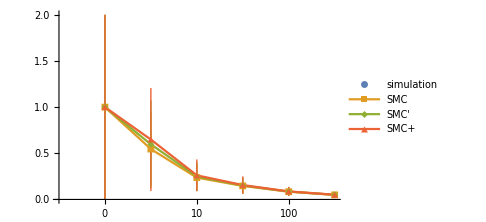
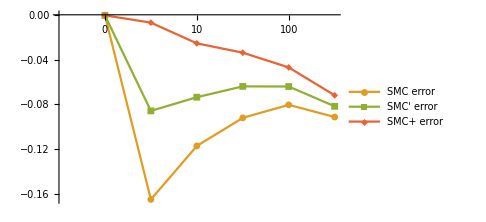
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[{meanVars,meanVarsSimple,meanVarsIntermediate,meanVarsComplicated},Joined->{False,True,True,True},PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotLegends->{"simulation","SMC","SMC'","SMC+"},Ticks->ticks],ListPlot[{meanErrorRsSimple,meanErrorRsIntermediate,meanErrorRsComplicated},Joined->True,PlotMarkers->{Automatic,Small},ImageSize->Medium,PlotStyle->ColorData[97,"ColorList"][[2;;4]],PlotLegends->{"SMC error","SMC' error","SMC+ error"},Ticks->ticks]}}]
```

#### KL divergences

```mathematica
$epsilon=10*^-9;
binLocations=Table[Apply[Join,histogramsFlatten[[combinedParameterIdx,;;,;;,1]]],{combinedParameterIdx,Length[combinedParameters]}];
binHeights=Table[Apply[Join,histogramsFlatten[[combinedParameterIdx,;;,;;,2]]],{combinedParameterIdx,Length[combinedParameters]}]+$epsilon;
```

```mathematica
binLocationsOrdered=Table[Sort[binLocations[[combinedParameterIdx]]],{combinedParameterIdx,Length[combinedParameters]}];
binHeightsOrdered=Table[Permute[binHeights[[combinedParameterIdx]],FindPermutation[binLocations[[combinedParameterIdx]],binLocationsOrdered[[combinedParameterIdx]]]],{combinedParameterIdx,Length[combinedParameters]}];
```

```mathematica
stepSizes=Table[Differences[Join[{0},binLocationsOrdered[[combinedParameterIdx]]]],{combinedParameterIdx,Length[combinedParameters]}];
Dkls=Table[Table[{xValues[[combinedParameterIdx]],Total[binHeightsOrdered[[combinedParameterIdx]]*Log[binHeightsOrdered[[combinedParameterIdx]]/Table[prediction[binLocation,combinedParameters[[combinedParameterIdx]]],{binLocation,binLocationsOrdered[[combinedParameterIdx]]}]]*stepSizes[[combinedParameterIdx]]]},{combinedParameterIdx,Length[combinedParameters]}],{prediction,{simple,intermediate,complicated}}];
```

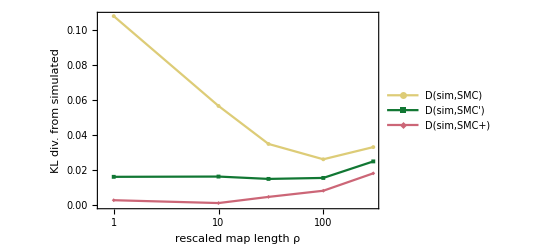

fig2.5 - DKLs.pdf

```mathematica
ListLogLinearPlot[Dkls,PlotRange->All,Joined->True,PlotLegends->{"D(sim,SMC)","D(sim,SMC')","D(sim,SMC+)"(*,"D(SMC+,SMC)"*)},Ticks->ticks,Frame->True,FrameLabel->{{style["KL div. from simulated"],None},{style["rescaled map length ρ"],None}},PlotStyle->cbfColors[[2;;4]],PlotMarkers->Table[{Automatic,Tiny},3]]
Export["fig2.5 - DKLs.pdf",%]
```